# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Práctica 6

Derivadas

```mathematica
f[x_]:=Sin[x]/Cos[x];
f'[x]
```

Sec[x]^2

```mathematica
f''[x]
```

2 Sec[x]^2 Tan[x]

### Derivada séptima de x

```mathematica
D[f[x],{x,7}]
```

272 Sec[x]^8+2880 Sec[x]^6 Tan[x]^2+1824 Sec[x]^4 Tan[x]^4+64 Sec[x]^2 Tan[x]^6

Derivada de f[x] 5 veces y después calcular f’’’’’[0]

```mathematica
D[f[x],{x,5}]/.x->0
```

16

### Comprobar derivadas hechas a mano

```mathematica
f'[x]
```

Sec[x]^2

Está bien

```mathematica
Sec[x]^2==(Cos[x]Cos[x]+Sin[x]Sin[x])/Cos[x]^2//Simplify
```

True

```mathematica
Simplify[%]
```

Sec[x]^2

### Derivación implícita

Para la derivación implícitas, escribimos la expresión especificando en este caso que y depende de x

```mathematica
D[x^2+y[x]^2==1,x]
```

2 x+2 y[x] y'[x]==0

### Recta tangente

La RT es la recta que pasa por un punto de la función y tiene su misma pendiente

```mathematica
f[x_]:=E^x Cos[x]
```

```mathematica
f[0]+f'[0](x-0)
```

1+x

```mathematica
r[x_]:=1+x
```

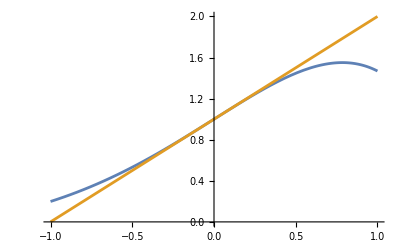

```mathematica
Plot[{f[x],r[x]},{x,-1,1}]
```

Estudio del signo, crecimiento y convexidad de una función

```mathematica
f[x_]:=x^3 -4x+8
```

Se estudia: el dominio de f, la continuidad de f, los ceros de f y se forman intervalos para evaluar f en ellos.